# LHS Calculation

```mathematica
params2 = {δt-> 0.1, τ-> 1,r0->1};
l=0.25;
rmax=20; (*12/l; (*SHOULD THIS DEPEND ON BIN SIZE?*)*)

ℤ=({{1, 0}, {0, -1}}); (*sigma z*)
ρ [θρ_,ϕρ_]:=({{(Cos[θρ/2])^2, Cos[θρ/2]*Sin[θρ/2]*Exp[-ⅈ*ϕρ]}, {Cos[θρ/2]*Sin[θρ/2]*Exp[ⅈ*ϕρ], (Sin[θρ/2])^2}}); (*Density matrix*)
𝕆=1/2(({{1, 0}, {0, 1}})+1*ℤ); (*Pi_i=Z with eigenvalue 1*)
ℙ=1/2(({{1, 0}, {0, 1}})-1*ℤ);(*Pi_i=Z with eigenvalue -1*)
𝔸[θa_, ϕa_]:=({{Cos[θa], Sin[θa]*Cos[ϕa]-ⅈ*Sin[θa]*Sin[ϕa]}, {Sin[θa]*Cos[ϕa]+ⅈ*Sin[θa]*Sin[ϕa], -Cos[θa]}});
𝔽[θf_,ϕf_]:=({{Cos[θf], Sin[θf]*Cos[ϕf]-ⅈ*Sin[θf]*Sin[ϕf]}, {Sin[θf]*Cos[ϕf]+ⅈ*Sin[θf]*Sin[ϕf], -Cos[θf]}});
𝕄$ra[r_,θa_,ϕa_]:=(√l)/(√1)*(δt/(2π*τ))^(1/4)*MatrixExp[-δt/(4*τ) (MatrixPower[r/1({{1, 0}, {0, 1}})-𝔸[θa,ϕa],2])]/.params2;
𝕄$ra$dag[r_,θa_,ϕa_]:=(√l)/(√1)*(δt/(2π*τ))^(1/4)*MatrixExp[-δt/(4*τ) (MatrixPower[-r/1({{1, 0}, {0, 1}})-𝔸[θa,ϕa],2])]/.params2;
𝕄[θf_,ϕf_]:=1/2(({{1, 0}, {0, 1}})+𝔽[θf,ϕf]); (*Pi_F with eigenvalue 1*)
ℕ[θf_,ϕf_]:=1/2(({{1, 0}, {0, 1}})-𝔽[θf,ϕf]);(*Pi_F with eigenvalue -1*)
x[r_,θρ_,ϕρ_,θa_,θf_,ϕf_,ϕa_]:=Log[2,Tr[ℕ[θf,ϕf].𝕄$ra[r,θa,ϕa].ρ[θρ,ϕρ].𝕄$ra$dag[r,θa,ϕa]]]/.params2;
y[r_,θρ_,ϕρ_,θa_,θf_,ϕf_,ϕa_]:=Log[2,Tr[𝕄[θf,ϕf].𝕄$ra[r,θa,ϕa].ρ[θρ,ϕρ].𝕄$ra$dag[r,θa,ϕa]]]/.params2;
(* Help with logs *)
LogHelpx[r_,θρ_,ϕρ_,θa_,θf_,ϕf_,ϕa_]:=If[(x[r,θρ,ϕρ,θa,θf,ϕf,ϕa])===Indeterminate,
0, (*True*)
x[r,θρ,ϕρ,θa,θf,ϕf,ϕa]]; (*False*)
LogHelpy[r_,θρ_,ϕρ_,θa_,θf_,ϕf_,ϕa_]:=If[(y[r,θρ,ϕρ,θa,θf,ϕf,ϕa])===Indeterminate,
0,
y[r,θρ,ϕρ,θa,θf,ϕf,ϕa]];
LogHelp1[θρ_,ϕρ_]:=If[(Log[2,Tr[𝕆.ρ[θρ,ϕρ]]]/.params2)===-∞,
0,
Log[2,Tr[𝕆.ρ[θρ,ϕρ]]]]/.params2;
LogHelp2[θρ_,ϕρ_]:=If[(Log[2,Tr[ℙ.ρ[θρ,ϕρ]]]/.params2)===-∞,
0,
Log[2,Tr[ℙ.ρ[θρ,ϕρ]]]]/.params2;
(* Entropies *)
ℍ$vnI[θρ_,ϕρ_]:=-Tr[𝕆.ρ[θρ,ϕρ]]*(LogHelp1[θρ,ϕρ])-Tr[ℙ.ρ[θρ,ϕρ]]*(LogHelp2[θρ,ϕρ]);   
ℍ$vnAF$singleR[r_,θρ_,ϕρ_,θa_,θf_,ϕf_,ϕa_]:=(
-(Tr[𝕄[θf,ϕf].𝕄$ra[r,θa,ϕa].ρ[θρ,ϕρ].𝕄$ra$dag[r,θa,ϕa]]*(LogHelpy[r,θρ,ϕρ,θa,θf,ϕf,ϕa]))
-(Tr[ℕ[θf,ϕf].𝕄$ra[r,θa,ϕa].ρ[θρ,ϕρ].𝕄$ra$dag[r,θa,ϕa]]*(LogHelpx[r,θρ,ϕρ,θa,θf,ϕf,ϕa]))
);
ℍ$vnAF[θρ_,ϕρ_,θa_,θf_,ϕf_,ϕa_]:=Sum[ℍ$vnAF$singleR[r,θρ,ϕρ,θa,θf,ϕf,ϕa],
{r,-rmax+(l/2),rmax-(l/2),l}];
LHS[θρ_,ϕρ_,θa_,θf_,ϕf_,ϕa_]:=ℍ$vnI[θρ,ϕρ]+ℍ$vnAF[θρ,ϕρ,θa,θf,ϕf,ϕa];
LHS$comp= Compile[{{θρ,_Real},{ϕρ,_Real},{θa,_Real},{θf,_Real},{ϕf,_Real},{ϕa,_Real}},
ℍ$vnI[θρ,ϕρ]+ℍ$vnAF[θρ,ϕρ,θa,θf,ϕf,ϕa]];
```

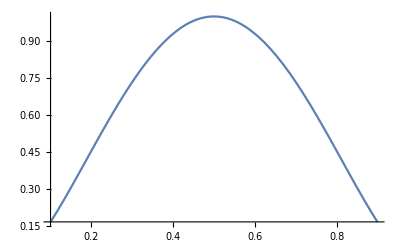
{0.033686,-Graphics-}

0.033686

```mathematica
Plot[ℍ$vnI[y*Pi,0], {y,0.1, 0.9}]
```

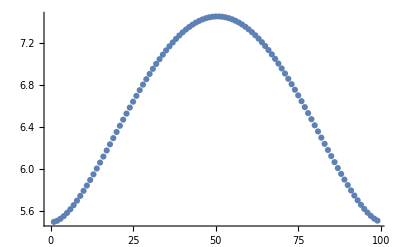
{116.268,-Graphics-}

```mathematica
ListPlot[ Table[Re[LHS[rho*3.14159,0.,1.99*3.14159,0.01*3.14159,0.,0.]],{rho,0.01,0.99,0.01}] ] //AbsoluteTiming
```

```mathematica
%47[[2]]
```

-Graphics-

```mathematica
Plot[Re[ℍ$vnAF[0.01*3.14159,0.,x*3.14159,0.25*3.14159,0.,0.]],{x,0.01,0.99}]//AbsoluteTiming
```

{37.4225,-Graphics-}

```mathematica
Monitor[
Table[LHS[tRho*3.14159,0.,ta*3.14159,tf*3.14159,0.,0.],
{ta,0.01,2.,0.1},{tf,0.01,1.,0.1},{tRho,0.01,1.,0.1}],
ProgressIndicator[ta/2*100 +tf*10 +tRho*1,{0,111}] ];
myData = %;
Export["/Users/jmonroe/Projects/entropicUncertainty/mathematica/LHS.txt", ExportString[Re[myData],"RawJSON","Compact"->True]]
```

```mathematica
ListDensityPlot3D[Re[myData]]
```

-Graphics3D-

/Users/jmonroe/Projects/entropicUncertainty/mathematica/LHS_A_0.5pi_F_0.5pi_xs.txt

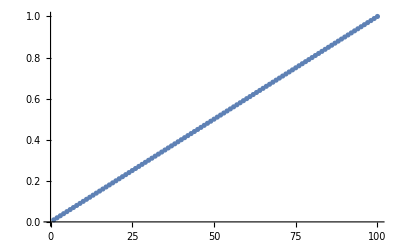

```mathematica
Monitor[
Table[LHS[tRho*3.14159,0.,0.5*3.14159,0.5*3.14159,0.,0.],
{tRho,0.01,1.,0.01}],
ProgressIndicator[tRho,{0,111}] ];
tmpData = %;
Export["/Users/jmonroe/Projects/entropicUncertainty/mathematica/LHS_A_0.5pi_F_0.5pi.txt", ExportString[Re[tmpData],"RawJSON","Compact"->True]]
ListPlot[tmpData]
```

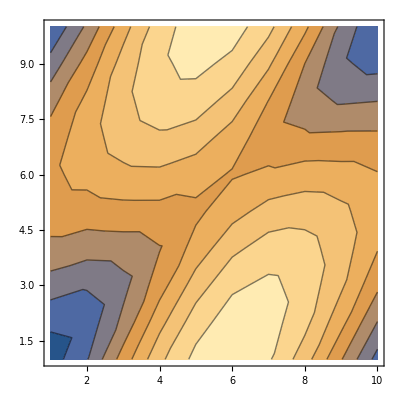

```mathematica
ListContourPlot[Re[ myData[[5]]] ,Contours->Table[5.25 + i*0.25,{i,0,10}]]
```

```mathematica
myData2D = Table[LHS[tRho*3.14159,0.,1*3.14159,tf*3.14159,0.,0.],
{tf,0.01,1.,0.1},{tRho,0.01,1.,0.1}];
ListContourPlot[Re[myData2D],Mesh-> All]
```

-Graphics-

```mathematica
Monitor[Table[LHS[tRho*3.14159,0.,2*3.14159,tf*3.14159,0.,0.],
{tf,0.01,1.,0.1},{tRho,0.01,1.,0.1}],
ProgressIndicator[ tf  ,{0,10}]];
myData2Dv2 = %;
```

$Aborted

```mathematica
ListPlot3D[Re[myData2Dv2]]
```

-Graphics3D-

## Checking why the LHS is imaginary

#### Expectation value of Tr[F AρA^†] is negative --> log[p] is imaginary

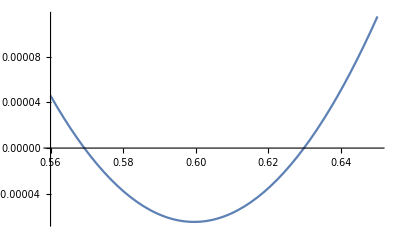

```mathematica
testFun[r_,θρ_,ϕρ_,θa_,θf_,ϕf_,ϕa_]:=(
Tr[ℕ[θf,ϕf].𝕄$ra[r,θa,ϕa].ρ[θρ,ϕρ].𝕄$ra$dag[r,θa,ϕa]]); 
Plot[testFun[1,0.6Pi, 0, 1Pi, x  Pi, 0,0], {x,0.56,0.65}]
```